```mathematica
DSolve[{x f''[x] + f'[x] == -ω^2/g f[x], f[L]==0}, f[x], x]//Simplify
```

{{f(x)→c_1 (0(2 √x ω)/(√g)-(0(2 √L ω)/(√g) 0(2 √x ω)/(√g))/(0(2 √L ω)/(√g)))}}

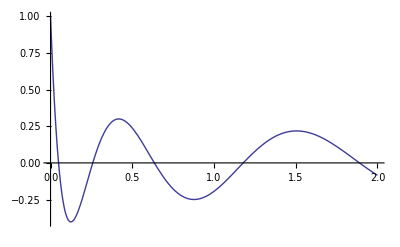

```mathematica
Plot[BesselJ[0, 2 * (√x)/(√9.8)ω]/.ω->17, {x, 0, 2}]
```